# BigWhamLink

## Simple Examples and illustrations of interface functions

Brice Lecampion

BigWhanLink is the Wolfram language interface to the BigWham C++ Library (© EPFL - 2016-2021). BigWham stands for Boundary InteGral equations With HierArchical Matrix.  
BigWhanLink uses the LTemplate package to produce the boiler plate WolframLibraryLink C code. (see https://github.com/szhorvat/LTemplate)

The first time the BigWhanLink paclet is loaded - LTemplate generates the code and compile a shared library which is then loaded. If the shared library already exists on your machine, no compilation is performed (such that in development mode you need to ensure you delete the shared library file to trigger recompilation if modifications have been performed on the C++ interface side)

Note that the root directory of the BigWhamLink git repo must be registered for Mathematica . This notebook is in this directory.

```mathematica
PacletDirectoryLoad[NotebookDirectory[]]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/}

```mathematica
<<BigWhamLink`
```

BigWhamLink`LTemplate`Classes`

Current directory is: /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source

Unloading library HmatExpressions ...

Generating library code ...

LTemplate-HmatExpressions.cpp already exists and will be overwritten.

Compiling library code ...

In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/LTemplate-HmatExpressions.cpp:9:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/HMatExpr.h:19:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/BigWham.h:17:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/il/il/Dynamic.h:19:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/il/il/container/dynamic/Dynamic.h:22:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/il/il/Type.h:19:
/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/il/il/container/dynamic/Type.h:211:1: warning: non-void function does not return a value in all control paths [-Wreturn-type]
}
^
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/LTemplate-HmatExpressions.cpp:9:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/HMatExpr.h:19:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/BigWham.h:21:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/hmat/hmatrix/Hmat.h:20:
/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/hmat/hmatrix/toHPattern.h:42:1: warning: non-void function does not return a value in all control paths [-Wreturn-type]
}
^
/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/hmat/hmatrix/toHPattern.h:68:1: warning: non-void function does not return a value in all control paths [-Wreturn-type]
}
^
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/LTemplate-HmatExpressions.cpp:9:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/LibraryResources/Source/HMatExpr.h:19:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/BigWham.h:30:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/elasticity/2d/ElasticHMatrix2DP0.h:19:
In file included from /Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/src/elasticity/2d/FullMatrixAssembly2D.h:15:
/opt/intel/compilers_and_libraries_2020/mac/tbb/include/tbb/tbb.h:21:9: warning: TBB Warning: tbb.h contains deprecated functionality. For details, please see Deprecated Features appendix in the TBB reference manual. [-W#pragma-messages]
#pragma message("TBB Warning: tbb.h contains deprecated functionality. For details, please see Deprecated Features appendix in the TBB reference manual.")
        ^
4 warnings generated.
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(cluster.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(PostProcessDDM_2d.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(PostProcessDDM_3d.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic3DR0_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic3DT0_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic2DP1_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(ElasticS3DP0_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic3DT6_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic3DR0_mode1Cartesian_element.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Mesh2D.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Mesh3D.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(FaceData.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(tensor_utilities_3DT6.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(h_potential_3DT6.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(Elastic3DR0_common.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)
ld: warning: object file (/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a(element_utilities.cpp.o)) was built for newer macOS version (10.15) than being linked (10.12)

We can check the  date of compilation for 
	1) the shared-library encapsulating the wolframLibraryLink interface entitled HmatExpressions (.dylib in mac, .so in linux)
	2) the static BigWham C++ library

```mathematica
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/interfaces/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Sat 11 Dec 2021 19:29:55GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Sat 11 Dec 2021 19:23:04GMT+1}

```mathematica
(* 
	a Function to get the memory used but not visible inside the wolfram kernel via MemoryInUse[] 
  results in Mbytes  (not super precise - but ok for order of magnitude
*)

MemoryTotal[]:= Block[{rr},
(* Return memory total by the mathematica process in Mbytes  / different than MemoryInUsep[*)
Switch[$SystemID,"Linux-x86-64",
rr=RunProcess[$SystemShell,"StandardOutput","pmap "<>ToString[$ProcessID]<>" | grep total 
      exit"]//ToString//StringSplit ;(*be careful return bits not Bytes*)
(StringTake[rr[[2]], ;;-2]//ToExpression) 1024/10^6. 
 ,"MacOSX-x86-64",
(* Mac OSX *)
rr=RunProcess[$SystemShell,"StandardOutput","
      top -r -l 1 -pid "<>ToString[$ProcessID]<>" | grep WolframKernel
      exit
      "]//ToString//StringSplit;
(*PID COMMAND %CPU TIME #TH #WQ #PORTS MEM PURG CMPRS PGRP PPID STATE BOOSTS %CPU_ME %CPU_OTHRS UID FAULTS COW MSGSENT MSGRECV SYSBSD
*)
(StringTake[rr[[8]] ,;;-2]//ToExpression) ]
]
```

### A simple flat crack in 2D plane-strain using P1 elements

In Mathematica, we devise a simple mesh for a crack between -1 and 1 along the x-axis. We mesh this crack with Nn elements using Piece-wise linear (P1) displacement discontinuity elements.
The kernel for such 2D element is instantiated via the string “2DP1” : 2D because it is the 2D  elastic kernel (plane-strain, but if you entered a modified poisson’s ratio works for plane-stress), and P1 because it is the P1 element.

This 2DP1 has displacement discontinuity unknowns located at the vertex of the element (not at the collocations points)
The collocation points are located inside the element  @ +-1/√2 on the unit segment [-1,1].
see A. Crawford and J. Curran. Higher-order functional variation displacement discontinuity elements. 19(3):143–148, 1982.

```mathematica
(* Mesh *)
Nn=600;  (* number of elements *)
coor=Table[{-1.+ 2i /Nn,0.},{i,0,  Nn}];  (*coordinates {x,y} of the vertex of the elements *)
conn=Table[{i,i+1},{i,1, Nn}];   (* mesh connectivity *)
```

As a side note, it is good practice to encapsulate the mesh description in an association object, i.e.

```mathematica
mesh= <|"Nodes"->coor,"Connectivity"->conn,"Nelts"->Length[conn],"Nnodes"->Length[coor],"DD order"->1,"Pressure order"->1(* this last one is for H-M coupling *)|>;
```

In order to construct the Hierarchical matrix object, beside a mesh, we need to specify:
- the kernel  as a string (“2DP1” here for P1 element)
- the material elastic properties : E (Young’s modulus) and ν  as a list  (+ possibly other parameters depending on the given kernel)
- Parameters for the H-mat compression (in that order): 
	maxleafsize (the maximum number of points for the deepest level of the cluster tree)  - must be an integer
	eta (float) defining the admissibility condition 
	eps_aca : the tolerance of the low rank approximation via ACA

```mathematica
ker="2DP1";"S3DP0";(*prop={1.0,0.3,1000.};*)

ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={1.0,0.3}; (* E, ν *)
```

```mathematica
m0=MemoryTotal[];
```

Now, we are ready to call the Hmat Construction -  the function is called toHMatExpr - it returns a BigWhamLink`LTemplate`Classes`HMatExpr instance (note we can have several instances per session if needed)

```mathematica
h1=toHMatExpr[coor,conn,ker,prop,ml,eta,eps]
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

BigWhamLink`LTemplate`Classes`HMatExpr[1]

```mathematica
tt=GetFullBlocks[h1]
```

calling getFullBlocks

preparing the Mtensors

preparing the sparse matrix

SparseArray[<1035000>, {2400, 2400}]

```mathematica
MatrixPlot[tt]
```

-Graphics-

```mathematica
mh=MemoryTotal[]-m0   (* how many Mb this H-mat takes place in memory *)
```

0

Now we can discuss the different functions available for such HmatExpr.
First, we can check the problem dimensions (how many dofs per nodes)

```mathematica
GetProblemDimension[h1]
```

2

```mathematica
GetSize[h1]
```

{2400,2400}

We can verify that it indeed corresponds to the kernel we asked for ;)

```mathematica
GetKernel[h1]=="2DP1"
```

True

Check the size of H-mat  (note with such element we have 2 *2 unknowns per element)

```mathematica
GetSize[h1]=={Nn 4, Nn 4}
```

True

Let’s now check the compression ratio

```mathematica
Cr=GetCompressionRatio[h1]
```

0.222188

We can estimate the ' size' in memory needed to store, the Hmat and the list of collocation points + permutation .
   So in Mbytes, before compression :

```mathematica
((Nn 4  )^2 +4  Nn  ) 8 /10^6.
```

46.0992

and after compression

```mathematica
( Cr(Nn 4  )^2 +4  Nn  ) 8 /10^6.
```

10.2576

which is not far off the check from the memory status  (actually smaller usually)

We can plot the Hierarchical matrix pattern (in the permuted state) - full-rank (in red) and low-rank blocks (green)

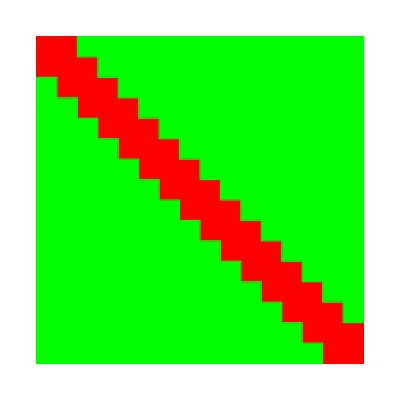

```mathematica
PlotHpattern[h1]
```

If you prefer  different colors....

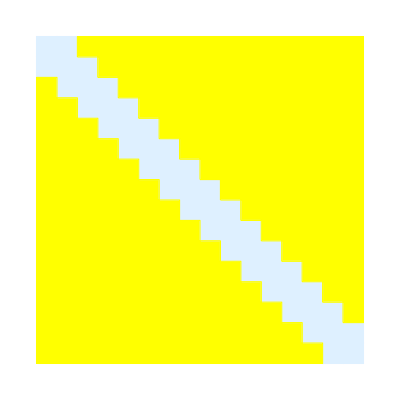

```mathematica
PlotHpattern[h1,Colors-> {LightBlue, Yellow}]
```

Let now retrieve the coordinates of the collocation points.

```mathematica
xycol=GetCollocationPoints[h1];
```

Let’s now do some H-dot product, we will plug in the solution for crack under uniform tensile loading.

```mathematica
Ep=prop[[1]]/(1-prop[[2]]^2); (* Plane YME *)

(*myww=({0, 4/Ep √(1-#^2)}& /@ MovingAverage[coor[[;;,1]],2]) //Flatten;*)
xyedge =Flatten[(coor[[#]]&/@ (conn)),1]; (* the coordinates of the edge of each element where the DD are located -  *)

myww=({0, 4/Ep √(1-#^2)}& /@ xyedge[[;;,1]]) //Flatten; (* the  DD vector:  (dds,ddn) at each vertex *)
```

Let’s now do the dot product using the hierarchical matrix - we do a repeatedTiming to better estimate the computational cost:

```mathematica
a=Hdot[h1,myww] ;//RepeatedTiming
```

{0.000324305,Null}

We can also check that the memory does not leak...  let’s do multiple H-dot - here adjust according to the cost of a single Hdot. 
We calculate the change in memory. should be zero (or small variations)

```mathematica
mem0=MemoryTotal[];
stats=Table[
Table[Clear[a];a=Hdot[h1, myww];,4];ma=MemoryTotal[];
{i,ma-mem0},{i,1,30}];
```

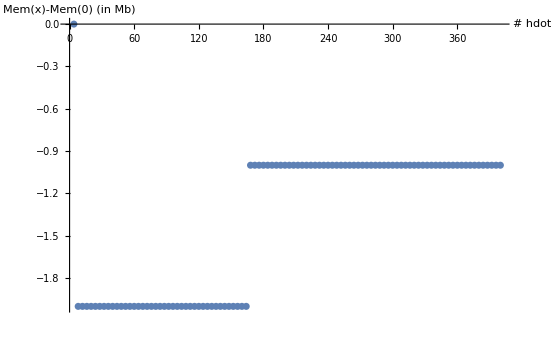

```mathematica
Show[ListPlot[ {#[[1]]4, #[[2]]}& /@ stats,AxesLabel->{"# hdot","Mem(x)-Mem(0) (in Mb)"}] ]
```

Let’s also check that the results of the dot corresponds to what we expect -  (uniform tensile load)

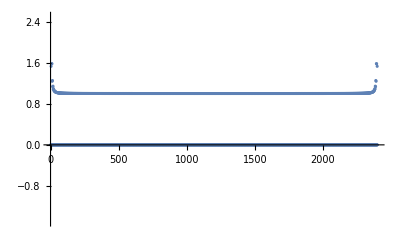

```mathematica
ListPlot[a]
```

```mathematica
Abs[Median[a[[2;;-1;;2]]]-1.]
```

0.000272948

```mathematica
Abs[Mean[a[[2;;-1;;2]]]-1.]
```

0.0251539

now we can ‘delete’ this H-matrix expression

```mathematica
h1=.
```

### 3D penny-shaped crack using Quadratic Triangle (T6)

```mathematica
Needs["NDSolve`FEM`"] (* Mathematica has great mesher *)
```

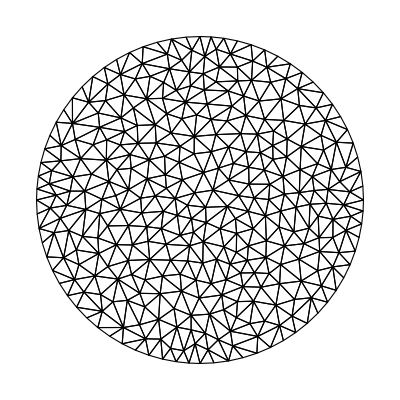

```mathematica
a=1; (* radius *) 
(* we do a very rough mesh *)
bmesh=ToBoundaryMesh[ImplicitRegion[x^2+y^2≤a^2,{x,y}],"MeshOrder"->1,"MaxBoundaryCellMeasure"->0.1,AccuracyGoal->1];

mesh=ToElementMesh[bmesh,"MeshOrder"->1,"RegionHoles"->None,MaxCellMeasure->.008]; (* It is important to specify "MeshOrder"-> 1 as our BEM solver has only a linear Triangle in terms of shape*)
 
coorOrder1=mesh["Coordinates"];
connOrder1=mesh["MeshElements"][[1]][[1]];
coorVertices=MapThread[Append,{coorOrder1,ConstantArray[ 0.,Length[coorOrder1]]}] ;
 
meshAs=<| "Nodes"-> coorVertices,"Connectivity"-> connOrder1 ,"Nelts"-> Dimensions[connOrder1,1][[1]]
,"Nnodes"->Length[coorVertices],"DD order"->2,"Pressure order"->1
|> ;
mesh["Wireframe"]
```

```mathematica
coor=coorVertices; conn=connOrder1;
```

```mathematica
ker="3DT6";
ml=100;
eta=3;
eps=0.001;
prop={1.0,0.3};
```

```mathematica
Mem0=MemoryTotal[];
```

```mathematica
h1=toHMatExpr[coor,conn,ker,prop,ml,eta,eps]
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

BigWhamLink`LTemplate`Classes`HMatExpr[2]

```mathematica
xy =GetCollocationPoints[h1];
perm=GetPermutation[h1]; (* permutation *)
```

```mathematica
GetSize[h1]== ( 3{ meshAs["Nelts"] 6, meshAs["Nelts"] 6})
```

True

```mathematica
GetSize[h1]
```

{11124,11124}

another function - testHmatExpr returns true if the instance is indeed a HmatExpression

```mathematica
testHmatExpr[h1]
```

True

```mathematica
GetCompressionRatio[h1]
```

0.26086

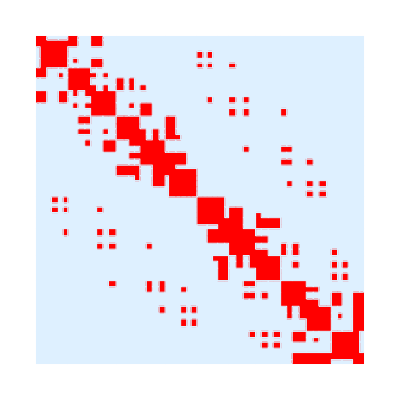

```mathematica
PlotHpattern[h1,Colors-> {Red,LightBlue}]
```

We will solve the crack problem as an example to show few additional features.

```mathematica
(* the analytical opening of a Penny-shaped fracture under tensile loading *)
Ep=prop[[1]]/(1-prop[[2]]^2);
xycol=GetCollocationPoints[h1];
(* --- here we need  the edge not the collocation points --*)
listr=√((#[[1]])^2+(#[[2]])^2)& /@ xycol[[;;,{1,2}]];
```

```mathematica
(* The tensile uniform loading *)
F=ConstantArray[0.,GetSize[h1][[1]]];
F[[3;;-1;;3]]=1.;
```

Let’s do some timing checks to see the timing of the Hdot

```mathematica
Hdot[h1,F];//RepeatedTiming
```

{0.01347,Null}

we create a function encapsulating the Hierarchical matrix instance to have a linear operator f(x) = H.x

```mathematica
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
```

```mathematica
FSB=GetFullBlocks[h1];
```

calling getFullBlocks

preparing the Mtensors

preparing the sparse matrix

We can use a Krylov iterative solver using as preconditioner an ILUT of the full blocks

```mathematica
(* ILU 0 PREconditioner *)
data=SparseArray`SparseMatrixILU[FSB,Method-> "ILUT","FillIn"->6,"Tolerance"-> 10^-5.];
prec=x↦SparseArray`SparseMatrixApplyILU[data,x];
```

```mathematica
{sol,stats}=Reap@LinearSolve[fdot,F,Method->{"Krylov",{"Method"-> "GMRES"(*"BiCGSTAB"*),"Preconditioner"->prec,"PreconditionerSide"->Right,(*"StartingVector"->v0,*)"Tolerance"->10^-5.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
```

```mathematica
(* We compare only the solution at the vertex of the mesh ---- lazy to compute at mid-edge ;( *)
```

```mathematica
stats[[1]]//Length
```

7

```mathematica
listr=√((#[[1]])^2+(#[[2]])^2)& /@ Flatten[ coor[[#,{1,2}]] & /@connOrder1  ,1];
```

```mathematica
ww=sol[[3;;-1;;3]];
wn=Table[ww[[  {1,2,3}+ (i-1) 6]],{i,1,Dimensions[connOrder1][[1]] }]//Flatten;
```

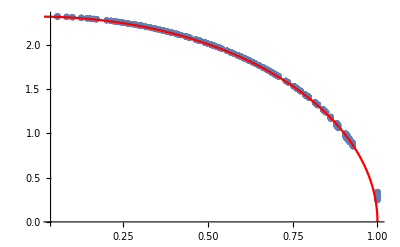

```mathematica
Show[ListPlot[Transpose[{listr,wn}],PlotRange->All,PlotMarkers->Automatic], Plot[8/(π (prop[[1]]/(1-prop[[2]]^2) ))√(1-x^2),{x,0,1},PlotStyle->Red] ]
```

```mathematica
abserr=Abs[wn-(8/(π (prop[[1]]/(1-prop[[2]]^2) ))√(1-#^2)& /@ listr)];
```

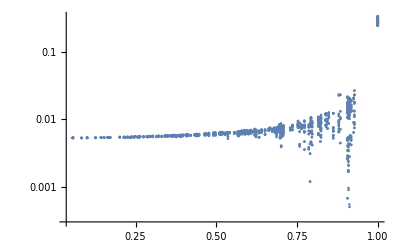

```mathematica
ListLogPlot[Transpose[{listr,abserr}],PlotRange->All]
```

```mathematica
{Median[abserr],Mean[abserr],Max[abserr]}
```

{0.00664686,0.0371559,0.338087}

```mathematica
h1=.
```